```mathematica
(* 1.1.3.2 *)
-Graphics-
(* Условие *)
-Graphics-
-Graphics-
(* Решение *)
(* 1. Уравнения Гамильтона *)
(* Дана функция Гамильтона заряженной частицы в пересекающихся магнитном и электрических полях. Запишем. *)
```

```mathematica
ℋ = 1/2(Px[t] - y[t] Subscript[H, z])^2 + 1/2(Py[t]+ x[t] Subscript[H, z])^2 + Ε x[t]
```

Ε x[t]+1/2 (Py[t]+H_z x[t])^2+1/2 (Px[t]-H_z y[t])^2

```mathematica
(* Распишем уравнения Гамильтона для данной  системы *)
∂_t x[t] == ∂_Px[t] ℋ
∂_t Px[t] == -∂_x[t] ℋ
∂_t y[t] == ∂_Py[t] ℋ
∂_t Py[t] == -∂_y[t] ℋ
```

x'[t]==Px[t]-H_z y[t]

Px'[t]==-Ε-H_z (Py[t]+H_z x[t])

y'[t]==Py[t]+H_z x[t]

Py'[t]==H_z (Px[t]-H_z y[t])

```mathematica
(* Далее, найдем решения данных уравнений *)
FullSimplify[DSolve[{D[x[t], t] == D[ℋ, Px[t]],D[Px[t], t] == -D[ℋ, x[t]],D[y[t], t] == D[ℋ, Py[t]],D[Py[t], t] == -D[ℋ, y[t]],x[0] ==0, Px[0] ==1,y[0]==0,Py[0]==0},{x[t],Px[t],y[t],Py[t]},t]]
```

{{Px[t]→1/4 (2-2 t Ε+2 Cos[2 t H_z]-(Ε Sin[2 t H_z])/H_z),Py[t]→1/2 (Sin[2 t H_z]-(Ε Sin[t H_z]^2)/H_z),x[t]→(-Ε Sin[t H_z]^2+Sin[2 t H_z] H_z)/(2 H_z^2),y[t]→(Ε Sin[2 t H_z]-2 (-1+t Ε+Cos[2 t H_z]) H_z)/(4 H_z^2)}}

```mathematica
(* 2. Далее, переходим к рассмотрению конфигурационного пространства *)
(* Теперь построим траекторию частицы в начальном конфигурационном пространстве, то есть координатном пространстве x[t], y[t] *)
ParametricPlot3D[{(-Ε Sin[t Subscript[H, z]]^2+Sin[2 t Subscript[H, z]] Subscript[H, z])/(2 Subscript[H, z]^2),(Ε Sin[2 t Subscript[H, z]]-2 (-1+t Ε+Cos[2 t Subscript[H, z]]) Subscript[H, z])/(4 Subscript[H, z]^2),z0}/.{Subscript[H, z]->2.5,Ε->1.2,z0->1},{t,0,20}] (* Происходит закручивание траектории частицы из-за наличия в данном пересечении полей магнитного поля, а у частицы наличия скорости и заряда *)
```

-Graphics3D-

```mathematica
(* 3.Фазовое пространство *)
```

```mathematica
(* В фазовом пространстве траектория относительно пар координат будет следующей: x[t], Px[t]; y[t], Py[t] *)
```

```mathematica
ParametricPlot[{(-Ε Sin[t Subscript[H, z]]^2+Sin[2 t Subscript[H, z]] Subscript[H, z])/(2 Subscript[H, z]^2),1/4 (2-2 t Ε+2 Cos[2 t Subscript[H, z]]-(Ε Sin[2 t Subscript[H, z]])/Subscript[H, z])}/.{Subscript[H, z]->2.5,Ε->1.2},{t,0,10}]
```

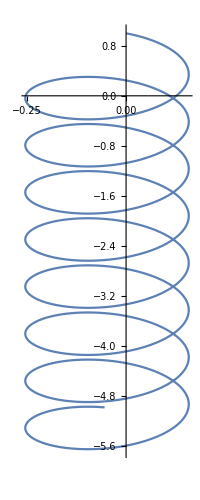

```mathematica
(* Траектория в фазовом пространстве x[t], Px[t] выглядит следующим образом *)
```

```mathematica
ParametricPlot[{(Ε Sin[2 t Subscript[H, z]]-2 (-1+t Ε+Cos[2 t Subscript[H, z]]) Subscript[H, z])/(4 Subscript[H, z]^2),1/2 (Sin[2 t Subscript[H, z]]-(Ε Sin[t Subscript[H, z]]^2)/Subscript[H, z])}/.{Subscript[H, z]->2.5,Ε->1.2},{t,0,10}]
```

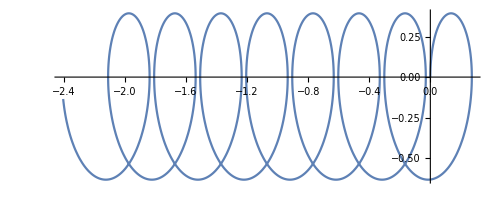

```mathematica
(* Траектория в фазовом пространстве y[t], Py[t] выглядит следующим образом *)
```

```mathematica
(* Причиной незамкнутости траектории является то что при раскрытии скобок в функции Гамильтона присутствуют произведения пар фазовых координат Py[t]*x[t] и Px[t] * y[t] в связи с чем появляется связь разных координат и импульсов, поэтому траектории двух фазовых пространств начинают влиять друг на друга, следавтельно начинает колебаться энергия *)
```

```mathematica
(* 4. Перейдем к повороту фазового пространства *)
(* Заметим, что повороту фазового пространства для координаты x на π/2 соответствует изменение пары координат x[t], Px[t] на пару Px[t],-x[t]*)
```

```mathematica
ℋ1 =  1/2(-x[t] - y[t] Subscript[H, z])^2 + 1/2(Py[t]+ Px[t] Subscript[H, z])^2 + Ε Px[t]
```

Ε Px[t]+1/2 (Py[t]+Px[t] H_z)^2+1/2 (-x[t]-H_z y[t])^2

```mathematica
(* Преимущество преобразования состоит в том, что после раскртия скобок больше нет произведений импульса на координату, в связи с чем и пропадает связь между компонентами влияющими на потенциальную и кинетическую энергию соответствено, что значительно упрощает изучение динамики частицы. Но есть один момент данного преобразования - появляются произведения различных координат и импульсов, которые не позволяют выразить функцию Гамильтона, как сумму двух независимых функций, отсюда следует необходимость нахождения канонического поворота, который как раз и позволит выполнить данное разбиение *)
```

```mathematica
(* 4.Разбиение функции Гамильтона на 2 независимые части* )
(* Сделаем поворот преобразованной системы фазовых координат *)
```

```mathematica
x[t]=-Sin[θ] η[t]+Cos[θ] ξ[t]
y[t]=Cos[θ] η[t]+Sin[θ] ξ[t]
```

-Sin[θ] η[t]+Cos[θ] ξ[t]

Cos[θ] η[t]+Sin[θ] ξ[t]

```mathematica
(* Матрица Якоби для поворота *)
J={{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}
MatrixForm[J]
```

{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}

(Cos[θ] | -Sin[θ]
Sin[θ] | Cos[θ])

```mathematica
(* Но после преобразования координат, необходимо преобразовать и импульсы. Сделаем это с помощью транспонирования обратной матрицы Якоби *)
({{Px[t]}, {Py[t]}})==Transpose[FullSimplify[Inverse[J]]].({{Pξ[t]}, {Pη[t]}})
```

True

```mathematica
Px[t]=Cos[θ] Pξ[t]-Pη[t] Sin[θ]
Py[t]=Cos[θ] Pη[t]+Pξ[t] Sin[θ]
```

Cos[θ] Pξ[t]-Pη[t] Sin[θ]

Cos[θ] Pη[t]+Pξ[t] Sin[θ]

```mathematica
(* Необходимо, чтобы наши преобразования оставались каноническими, то есть в процессе преобразования уравнение Гамильтона оставалось неизменным, то есть необходимо сделать проверку при помощи скобок Пуассона *)
PB[M_, N_] :=D[M, η[t]] D[N, Pη[t]] - D[N, η[t]] D[N, Pη[t]] + D[M, ξ[t]] D[N, Pξ[t]] - D[N, ξ[t]] ∂_Pξ[t] N (*Скобки Пуассона*)
```

```mathematica
Simplify[PB[-Sin[θ] η[t]+Cos[θ] ξ[t], Cos[θ] Pξ[t]-Pη[t] Sin[θ]]] ==1(* Проверяем равенство скобок Пуассона единицы для x[t], Px[t] *)
```

True

```mathematica
Simplify[PB[Cos[θ] η[t]+Sin[θ] ξ[t], Cos[θ] Pη[t]+Pξ[t] Sin[θ]]]==1 (* Проверяем равенство скобок Пуассона единице для y[t], Py[t] *)
```

True

```mathematica
(* Поскольку преобразования остались каноническими, значит и уравнения Гамильтона остаются верными *)
```

```mathematica
(* Получим функцию Гамильтона в повернутой и преобразованный системе координат *)
ℋ1/.{x[t]->-Sin[θ] η[t]+Cos[θ] ξ[t],Px[t] ->Cos[θ] Pξ[t]-Pη[t] Sin[θ],y[t]->Cos[θ] η[t]+Sin[θ] ξ[t],Py[t] ->Cos[θ] Pη[t]+Pξ[t] Sin[θ]}
```

Ε (Cos[θ] Pξ[t]-Pη[t] Sin[θ])+1/2 (Cos[θ] Pη[t]+Pξ[t] Sin[θ]+(Cos[θ] Pξ[t]-Pη[t] Sin[θ]) H_z)^2+1/2 (Sin[θ] η[t]-Cos[θ] ξ[t]-H_z (Cos[θ] η[t]+Sin[θ] ξ[t]))^2

```mathematica
FullSimplify[ℋ1]
```

1/2 (2 Ε (Cos[θ] Pξ[t]-Pη[t] Sin[θ])+(Pξ[t] (Sin[θ]+Cos[θ] H_z)+Pη[t] (Cos[θ]-Sin[θ] H_z))^2+((-Sin[θ]+Cos[θ] H_z) η[t]+(Cos[θ]+Sin[θ] H_z) ξ[t])^2)

```mathematica
(* Опять же, для разбиения функции Гамильтона, необходимо найти такой угол поворота θ, что все произведения Pη[t]*Pξ[t], η[t]*ξ[t] обращались в ноль *)
```

```mathematica
(1/2 Pη[t] Pξ[t] (2 Cos[2 θ] Subscript[H, z]-Sin[2 θ] (-1+Subscript[H, z]^2))) (* Произведение Pη[t]*Pξ[t] *)
```

1/2 Pη[t] Pξ[t] (2 Cos[2 θ] H_z-Sin[2 θ] (-1+H_z^2))

```mathematica
(1/2 (2 Cos[2 θ] Subscript[H, z]+Sin[2 θ] (-1+Subscript[H, z]^2)) η[t] ξ[t])(* Произведение η[t]*ξ[t] *)
```

1/2 (2 Cos[2 θ] H_z+Sin[2 θ] (-1+H_z^2)) η[t] ξ[t]

```mathematica
Solve[2  Subscript[H, z]-Tan[2 θ] (-1+Subscript[H, z]^2)==0,θ]/.C[1] ->0
```

{{θ→1/2 ArcTan[(2 H_z)/(-1+H_z^2)]}}

```mathematica
Solve[2  Subscript[H, z]+Tan[2 θ] (-1+Subscript[H, z]^2)==0,θ]/.C[1] ->0
```

{{θ→-1/2 ArcTan[(2 H_z)/(-1+H_z^2)]}}

```mathematica
(* В общем случае такого угла не существует, поэтому сделаем хитрость : произведем переход в новое фазовое пространство, но с применением как поворота, так и сжатия *)
ℋ2 =  1/2(x[t] + y[t] Subscript[H, z])^2 + 1/2(Py[t]+ Px[t] Subscript[H, z])^2 + Ε Px[t]/.{Subscript[H, z]->1,Ε ->1}(* Функция Гамильтона в этом пространстве *)
```

Px[t]+1/2 (Px[t]+Py[t])^2+1/2 (x[t]+y[t])^2

```mathematica
(*Попробуем сделать замену*)
```

```mathematica
Z[t] = (x[t]+y[t])/(√2)
 Pz[t] = (Py[t]+ Px[t])/(√2)
```

```mathematica
(* Воспользуемя скобками Пуассона для проверки преобразование *)
```

```mathematica
D[Z[t], x[t]]D[Pz[t], Px[t]]-D[Z[t], Px[t]]D[Pz[t], x[t]]+ D[Z[t], y[t]]D[Pz[t], Py[t]]-D[Z[t], Py[t]]D[Pz[t], y[t]]==1
```

True

```mathematica
(* Скобки Пуассона равны единице, отсюда слдует, что преобразование каноническое *)
```

```mathematica
ℋ3 =Pz[t] √2-Py[t]+1/2 (Pz[t] √2)^2+1/2 (Z[t] √2)^2
```

√2 Pz[t]+Pz[t]^2-Cos[θ] Pη[t]-Pξ[t] Sin[θ]+Z[t]^2

```mathematica
(* Мы задали новую функцию Гамильтона.В ней нет произведения функций от времени разных координат и импульсов, но есть один импульc, не входящий в фазовое пространство z[t] Pz[t]. *)
```

```mathematica
(*Теперь запишем уравнения Гамильтона для этой функции и решим их*)
```

```mathematica
FullSimplify[DSolve[{D[Z[t], t] == D[ℋ3, Pz[t]] ,D[Pz[t], t] ==-D[ℋ3, Z[t]] ,D[y[t], t] == D[ℋ3, Py[t]],D[Py[t], t] == -D[ℋ3, y[t]], Z[0]==0,Pz[0]==1},{Z[t],Pz[t],Py[t],y[t]},t]]
```

{{Pz[t]→-1/(√2)+(1+1/(√2)) Cos[2 t],Z[t]→(2+√2) Cos[t] Sin[t],y[t]→-t+C[3],Py[t]→C[4]}}

```mathematica
(* Как видно, в решении уравнения Гамильтона импульс Py оказался постоянным, отсюда следует независимость движения в фазовом пространстве z[t], Pz[t] не зависит от Py *)
```

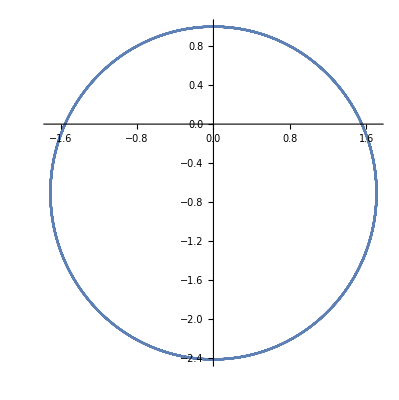

```mathematica
(*Траектория движения в фазовом пространстве z[t], Pz[t] выглядит следующим образом*)
ParametricPlot[{(2+√2) Cos[t] Sin[t],-1/(√2)+(1+1/(√2)) Cos[2 t]},{t,0,20}]
```

```mathematica
(* Траектория стала замкнутой, отсюда следует, что пропала энергетическая связь магнитного и электрического поля *)
```